```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->18};
plotStyles={
{Darker@Blue,AbsoluteThickness[2]},
{Darker@Green,AbsoluteThickness[2],Dashed},
{Darker@Red,AbsoluteThickness[2],DotDashed},
{Black,AbsoluteThickness[2],Dotted},
{Purple,AbsoluteThickness[2],Dashed}
};
```

## Example: Neutral Entropy Plot

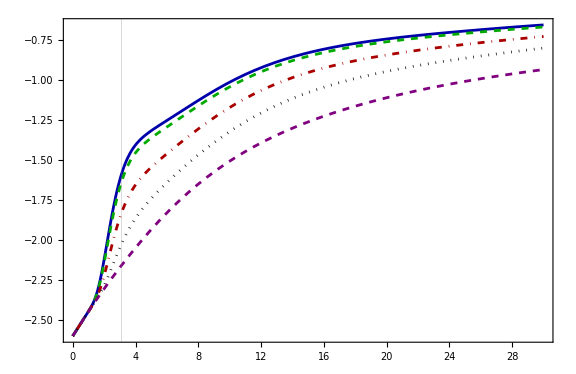

```mathematica
folder = "~/dev/julia/Chihuahua/output/";
impactParameters={0,2,5,8};
files =(ToString[StringForm["neutral_oblate_dx_``.h5",ToString[#]]]&/@impactParameters)~Join~{"single_neutral_oblate.h5"};
labels = (ToString[StringForm["\\delta x = ``",ToString[#]]]&/@impactParameters)~Join~{"\\mathrm{Two Blobs}"};
functions = Interpolation[Import[folder<>#,{"Datasets","/out_vars_avg/neutral_entropy"}]]&/@files;
stuffToPlot=Through[functions[t]];stuffToPlot[[-1]] =2 stuffToPlot[[-1]] ;(*Here double the entropy of a single blob*)

Plot[stuffToPlot, {t, 0,30},
Frame->True,Axes->False,PlotStyle->plotStyles,FrameStyle->BlackFrame,BaseStyle->texStyle,FrameLabel->MaTeX[{"t","\\frac{S_1}{L_xL_yL_z}","",""},Magnification->1.7],AspectRatio->0.65,PlotLegends->Placed[LineLegend[MaTeX[labels,Magnification->1.4], Spacings -> 0],{{0.65,0.1},{0,0}}],GridLines->{{3.1120640431758946},None}, ImageSize->Large]
```

## Example: Snapshot

```mathematica
folder = "~/dev/julia/Chihuahua/output/";
file = "charged_oblate_dx_2.h5";
frame = 4;
xx =Import[folder<>file,{"Datasets","/Grid/x"}];
zz=Import[folder<>file,{"Datasets","/Grid/z"}];
mm =Import[folder<>file,{"Datasets","/out_vars_xz/mass"}][[frame]];
f=Interpolation@Flatten[Table[{{xx[[i]], zz[[j]]}, mm[[j,i]]}, {i, Length[xx]}, {j, Length[zz]}], 1];

DensityPlot[f[x,z], {x, -50,50}, {z, -50,50},
 PlotRange->All, PlotPoints->50, ColorFunction->"SunsetColors", PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{318,15},LegendLayout->"Row",LabelStyle->{texStyle,Black}],{{0.945,1},{1,0.88}}],FrameStyle->BlackFrame,BaseStyle->texStyle,FrameLabel->MaTeX[{"x","z","",""},Magnification->1.7],Axes->False,ImageSize->400]
```

-Graphics-